```mathematica
y[x_,c0_,c1_,c2_,c3_]:= c0+c1 x+c2 x^2+c3 x^3
```

```mathematica
Solve[y[0]==0 && y'[0]==0 ,{c0,c1}]
```

{}

```mathematica
?Solve
```

```mathematica
ClearAll[y]
y[f_,l_,Ε_,Ι_][x_]:=f/(Ε Ι)(l x^2/2-x^3/6)
```

```mathematica
Block[{l=3,Ε=200 10^9, Ι=60.7 10^-6,f=20 10^3},
y[f,l,Ε,Ι]'[l] 180/π
]
```

0.424763

```mathematica
y[x,f,l,Ε,Ι]
```

(f ((l x^2)/2-x^3/6))/(Ε Ι)

```mathematica
0.0222/3
```

0.0074

```mathematica
<<Notation`
```

Join::incpt: Incompatible elements in Join[<|intt→RowBox[{∫,RowBox[{■,RowBox[{ⅆ,□}]}]}],«46»,cY→TemplateBox[{},CombinatorY]|>,«5»,{«1»}] cannot be joined.

Join::incpt: Incompatible elements in Join[<|intt→RowBox[{∫,RowBox[{■,RowBox[{ⅆ,□}]}]}],«46»,cY→TemplateBox[{},CombinatorY]|>,«6»,{«1»}] cannot be joined.

```mathematica
Symbolize[Subscript[x_, y_]]
```

```mathematica
sol=DSolve[y''[Subscript[X, 1]]==w0/(2 Ε Ι)(l- Subscript[X, 1])^2 &&  y[0]==0 && y'[0]==0,y[Subscript[X, 1]],Subscript[X, 1]]//Simplify
```

{{y[X_1]→(w0 X_1^2 (6 l^2-4 l X_1+X_1^2))/(24 Ε Ι)}}

```mathematica
ysol[Subscript[X, 1]:_]:=Evaluate[y[Subscript[X, 1]]/.sol[[1]]]
```

```mathematica
ysol[l]
```

(l^4 w0)/(8 Ε Ι)

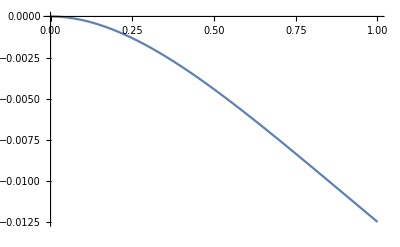

```mathematica
Block[{l=1,w0=0.1},
Plot[-ysol[Subscript[X, 1]],{Subscript[X, 1],0,l}]]
```

```mathematica
?DSolve
```

```mathematica
ysol[X]
```

y[X]

```mathematica
Needs["Notation`"]
```

Join::incpt: Incompatible elements in Join[<|intt→RowBox[{∫,RowBox[{■,RowBox[{ⅆ,□}]}]}],«46»,cY→TemplateBox[{},CombinatorY]|>,{notation→«1»,«7»},«8»,«4»] cannot be joined.

Join::incpt: Incompatible elements in Join[<|intt→RowBox[{∫,RowBox[{■,RowBox[{ⅆ,□}]}]}],«46»,cY→TemplateBox[{},CombinatorY]|>,{notation→«1»,«7»},«8»,«5»] cannot be joined.

```mathematica
Symbolize[Subscript[x_, y_]]
```

```mathematica
(*sol1=DSolve[y''[Subscript[X, 1]]==w0/(2 Ε Ι)(l- Subscript[X, 1])^2 &&  y[0]==0 && y'[0]==0,y[Subscript[X, 1]],Subscript[X, 1]]//Simplify
*)sol2=DSolve[y''[Subscript[X, 1]]==w0/(2 Ε Ι)(l- Subscript[X, 1])^2 -(w0 l)/(Ε Ι) (l-Subscript[X, 1]) &&  y[l]==0 && y'[0]==0,y[Subscript[X, 1]],Subscript[X, 1]]//Simplify
```

{{y[X_1]→(w0 (5 l^4-6 l^2 X_1^2+X_1^4))/(24 Ε Ι)}}

```mathematica
(*y1[Subscript[X, 1]:_]:=Evaluate[y[Subscript[X, 1]]/.sol1[[1]]]*)
y2[Subscript[X, 1]:_]:=Evaluate[y[Subscript[X, 1]]/.sol2[[1]]]
```

```mathematica
y2[s]
```

-((l-s)^3 (3 l+s) w0)/(24 Ε Ι)

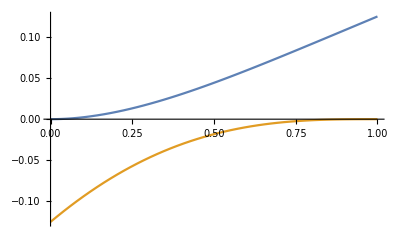

```mathematica
Block[{w0=1,Ε=1,Ι=1,l=1},Plot[{y1[s],y2[s]},{s,0,l}]]
```

```mathematica
(w0/(2 Ε Ι)(l- Subscript[X, 1])^2 -(w0 l)/(Ε Ι) (l-Subscript[X, 1]))//Simplify
```

-(w0 (l-X_1) (l+X_1))/(2 Ε Ι)

```mathematica
Integrate[Subscript[w, 0]/l^2(Subscript[X, 1]+ξ)^2 ξ,{ξ,0, l-Subscript[X, 1]}]//Simplify
```

(w_0 (3 l^4-4 l^3 X_1+X_1^4))/(12 l^2)

```mathematica
Subscript[w, 0]/l^2((Subscript[X, 1]^2(l-Subscript[X, 1])^2)/2+(l-Subscript[X, 1])^4/4+(2 Subscript[X, 1](l-Subscript[X, 1])^3)/3)//Simplify
```

(w_0 (3 l^4-4 l^3 X_1+X_1^4))/(12 l^2)

```mathematica
Integrate[Integrate[(Subscript[w, 0] (3 l^4-4 l^3 Subscript[X, 1]+Subscript[X, 1]^4))/(12 l^2),Subscript[X, 1]],Subscript[X, 1]]
```

(w_0 (15/2 l^4 X_1^2-10/3 l^3 X_1^3+X_1^6/6))/(60 l^2)

```mathematica
sol1=DSolve[y''[Subscript[X, 1]]==(Subscript[w, 0] (3 l^4-4 l^3 Subscript[X, 1]+Subscript[X, 1]^4))/(12 l^2) && y[0] ==0 && y'[0]==0,y[Subscript[X, 1]],Subscript[X, 1]]//Simplify
(*sol2=DSolve[y''[Subscript[X, 1]]==(Subscript[w, 0] (3 l^4-4 l^3 Subscript[X, 1]+Subscript[X, 1]^4))/(12 l^2) && y[0] ==0 && y'[0]==0,y[Subscript[X, 1]],Subscript[X, 1]]*)
```

{{y[X_1]→(w_0 X_1^2 (45 l^4-20 l^3 X_1+X_1^4))/(360 l^2)}}

1

1

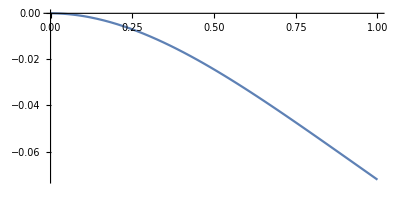

```mathematica
Subscript[w, 0]=1
l=1
Plot[-(Subscript[w, 0] (45 l^4 Subscript[X, 1]^2-20 l^3 Subscript[X, 1]^3+Subscript[X, 1]^6))/(360 l^2),{Subscript[X, 1],0,l},AspectRatio->1/2]
```

```mathematica
Integrate[X1-Y1,{X1,Y1,l}]//FullSimplify
```

1/2 (l-Y1)^2